## Verifying Some Graphs For elliptical Path

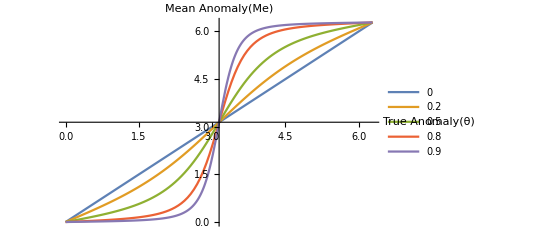

```mathematica
Clear["Global`*"]
e =  {0,0.2,0.5,0.8,0.9};
Me=2ArcTan[Sqrt[(1-e)/(1+e)]Tan[θ/2]]-(e Sqrt[1-e^2]Sin[θ])/(1+e Cos[θ]);
Me2 = Me+2 Pi;
h1= Plot[Me,{θ,0,Pi},PlotLegends->{e},AxesOrigin->{Pi,Pi},AxesLabel->{"True Anomaly(θ)","Mean Anomaly(Me)"}];
h2 = Plot[Me2,{θ,Pi,2 Pi}];
Show[h1,h2,PlotRange->All]
```

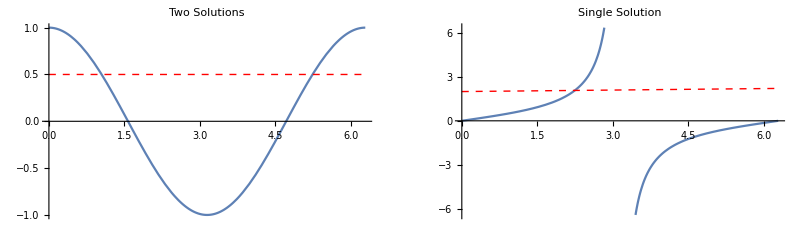

```mathematica
e = 0.7;
h3 = Plot[Cos[θ],{θ,0,2Pi},PlotLabel->"Two Solutions"];
h4 = Graphics[{Red,Dashed,Line[{{0,0.5},{2Pi,0.5}}]}];
h5 = Plot[Tan[θ/2],{θ,0,2Pi},Exclusions->{Pi},PlotLabel->"Single Solution"];
h6 =Graphics[{Red,Dashed,Line[{{0,2},{2Pi,2*ArcTan[2]}}]}];
GraphicsGrid[{{Show[h3,h4],Show[h5,h6]}},Frame->All]
```

```mathematica
Clear["Global`*"]
Me = Ea - e Sin[Ea];
Manipulate[
Plot[Me/.e->param,{Ea,0,2Pi},AxesLabel->{"Eccentric Anomaly(E)","Mean Anomaly (M_e)"},
ImageSize->600],{{param,0,"Eccintricity"},0,0.99}]
```